```mathematica
data1=Import["D:/Healing.txt",{"Data",{All},{1,2}}]
```

{{5,47},{10,67},{15,77},{20,83},{25,87},{30,89}}

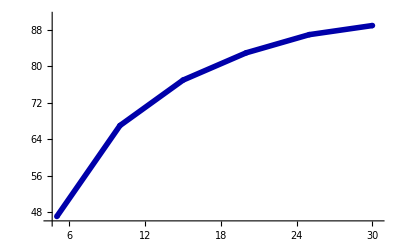

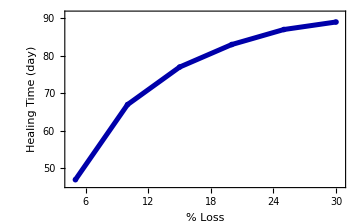

```mathematica
G2=ListLinePlot[data1,PlotMarkers->{Automatic,Medium},AxesStyle->Directive[Black,12],PlotRange->{{4.5,30.4},{45.8,91}},PlotStyle->{Darker[Blue],Thickness[0.01]}(*PlotStyle->{Darker[Blue],PointSize[0.05]}*),    FrameTicksStyle->Directive[Black,14]]
pl00=Show[G2,ImageSize->Medium,Frame->True,FrameLabel->{Style["% Loss",18(*,Bold*)],Style["Healing Time (day)",18(*,Bold*)]},FrameStyle->Directive[Black,12],FrameTicksStyle->Directive[Black,14],LabelStyle->Directive[(*Bold,*)Black,18,FontFamily->"Times New Roman"]]
```

```mathematica
pl2=Labeled[pl00,Style["(B)","Section",Black,FontFamily->"Times New Roman"],{{Top,Left}}]
```

-Graphics-(B)

```mathematica
Export["D:/Ratio3.eps",pl2]
```

D:/Ratio3.eps